```mathematica
Names[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,44885,System`Convert`NotebookMLDump`$XMLThreeArgBoxes,System`Convert`NotebookMLDump`$XMLTwoArgBoxes,System`Convert`NotebookMLDump`$XMLTwoArgKernelBoxes,System`FunctionZerosDump`$ZetaZeroMarker,FileFormatDump`$ZIPFORMATS,Integrate`$$a,Integrate`$$b,Integrate`$$c,System`Private`$$Failure2,System`Private`$$ParenForm,GeneralUtilities`EvaluationInformation`PackagePrivate`$$return,GeneralUtilities`EvaluationInformation`PackagePrivate`$$return$,GeneralUtilities`EvaluationInformation`PackagePrivate`$$time,GeneralUtilities`EvaluationInformation`PackagePrivate`$$time$,System`Convert`TeXImportDump`$$TNBLink,Integrate`$$u,Discrete`DivisorSumDump`$$var,System`Convert`MathMLDump`∅,\[SystemsModelDelay]}
 |  |  |  |

```mathematica
"\[SystemsModelDelay]"
```

\[SystemsModelDelay]

```mathematica
\[SystemsModelDelay]
```

\[SystemsModelDelay]

```mathematica
Information[\[SystemsModelDelay]]
```

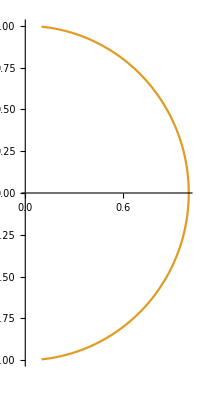

```mathematica
ParametricPlot[{
Normalize@{1,1},
Normalize@{1,2t},
Normalize@{1,2t} . Normalize@{1,1}
},{t, -5, 5}]
```

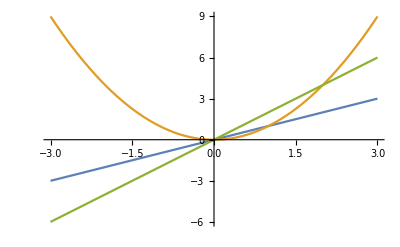

```mathematica
Plot[{x,x^2,1 2x},{x,-3,3}]
```

```mathematica
Sin[x^2]Sin[x]
```

Sin[x] Sin[x^2]

```mathematica
TrigReduce[Sin[x] Sin[x^2]]
```

1/2 (Cos[x-x^2]-Cos[x+x^2])

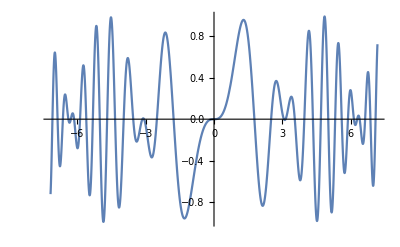

```mathematica
Plot[1/2 (Cos[x-x^2]-Cos[x+x^2]),{x,-7.1734425523214425,7.1734425523214425}]
```

```mathematica
DateValue[Today[], "Month"]
```

DateValue::arg: Argument DateObject[{2019,6,6},Day,Gregorian,-7.][] cannot be interpreted as a date or time input

DateValue[Day: Thu 6 Jun 2019[],Month]

```mathematica
DateValue[DateObject@Today[], "Month"]
```

DateValue::arg: Argument DateObject[DateObject[{2019,6,6},Day,Gregorian,-7.][]] cannot be interpreted as a date or time input

DateValue[DateObject[Day: Thu 6 Jun 2019[]],Month]

```mathematica
DateValue[Today, "Month"]
```

6

```mathematica
DateValue[Today, "MonthName"]
```

June

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
Transpose[{list["Dates"],list["Values"]}]
]
```

{{Thu 15 May 1997 00:00:00GMT-7.,1.96 $},{Fri 16 May 1997 00:00:00GMT-7.,1.73 $},{Mon 19 May 1997 00:00:00GMT-7.,1.71 $},{Tue 20 May 1997 00:00:00GMT-7.,1.64 $},{Wed 21 May 1997 00:00:00GMT-7.,1.43 $},{Thu 22 May 1997 00:00:00GMT-7.,1.40 $},{Fri 23 May 1997 00:00:00GMT-7.,1.50 $},{Tue 27 May 1997 00:00:00GMT-7.,1.58 $},{Wed 28 May 1997 00:00:00GMT-7.,1.53 $},{Thu 29 May 1997 00:00:00GMT-7.,1.51 $},5532,{Thu 23 May 2019 00:00:00GMT-7.,1 815.48 $},{Fri 24 May 2019 00:00:00GMT-7.,1 823.28 $},{Tue 28 May 2019 00:00:00GMT-7.,1 836.43 $},{Wed 29 May 2019 00:00:00GMT-7.,1 819.19 $},{Thu 30 May 2019 00:00:00GMT-7.,1 816.32 $},{Fri 31 May 2019 00:00:00GMT-7.,1 775.07 $},{Mon 3 Jun 2019 00:00:00GMT-7.,1 692.69 $},{Tue 4 Jun 2019 00:00:00GMT-7.,1 729.56 $},{Wed 5 Jun 2019 00:00:00GMT-7.,1 738.50 $}}
 |  |  |  |

```mathematica
GatherBy[
Out[17],
DateValue[First@#, "MonthName"]&]
```

{{{Thu 15 May 1997 00:00:00GMT-7.,1.96 $},{Fri 16 May 1997 00:00:00GMT-7.,1.73 $},{Mon 19 May 1997 00:00:00GMT-7.,1.71 $},{Tue 20 May 1997 00:00:00GMT-7.,1.64 $},{Wed 21 May 1997 00:00:00GMT-7.,1.43 $},{Thu 22 May 1997 00:00:00GMT-7.,1.40 $},{Fri 23 May 1997 00:00:00GMT-7.,1.50 $},{Tue 27 May 1997 00:00:00GMT-7.,1.58 $},{Wed 28 May 1997 00:00:00GMT-7.,1.53 $},{Thu 29 May 1997 00:00:00GMT-7.,1.51 $},458,{Mon 20 May 2019 00:00:00GMT-7.,1 858.97 $},{Tue 21 May 2019 00:00:00GMT-7.,1 857.52 $},{Wed 22 May 2019 00:00:00GMT-7.,1 859.68 $},{Thu 23 May 2019 00:00:00GMT-7.,1 815.48 $},{Fri 24 May 2019 00:00:00GMT-7.,1 823.28 $},{Tue 28 May 2019 00:00:00GMT-7.,1 836.43 $},{Wed 29 May 2019 00:00:00GMT-7.,1 819.19 $},{Thu 30 May 2019 00:00:00GMT-7.,1 816.32 $},{Fri 31 May 2019 00:00:00GMT-7.,1 775.07 $}},10,{1}}
 |  |  |  |

```mathematica
Table[
Map[Last,i],
{i, Out@17}]
```

{{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},5511,{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars},{-7.,USDollars}}
 |  |  |  |

```mathematica
Out[22][[1]]
```

{{Thu 15 May 1997 00:00:00GMT-7.,1.96 $},{Fri 16 May 1997 00:00:00GMT-7.,1.73 $},{Mon 19 May 1997 00:00:00GMT-7.,1.71 $},{Tue 20 May 1997 00:00:00GMT-7.,1.64 $},{Wed 21 May 1997 00:00:00GMT-7.,1.43 $},{Thu 22 May 1997 00:00:00GMT-7.,1.40 $},{Fri 23 May 1997 00:00:00GMT-7.,1.50 $},{Tue 27 May 1997 00:00:00GMT-7.,1.58 $},{Wed 28 May 1997 00:00:00GMT-7.,1.53 $},{Thu 29 May 1997 00:00:00GMT-7.,1.51 $},458,{Mon 20 May 2019 00:00:00GMT-7.,1 858.97 $},{Tue 21 May 2019 00:00:00GMT-7.,1 857.52 $},{Wed 22 May 2019 00:00:00GMT-7.,1 859.68 $},{Thu 23 May 2019 00:00:00GMT-7.,1 815.48 $},{Fri 24 May 2019 00:00:00GMT-7.,1 823.28 $},{Tue 28 May 2019 00:00:00GMT-7.,1 836.43 $},{Wed 29 May 2019 00:00:00GMT-7.,1 819.19 $},{Thu 30 May 2019 00:00:00GMT-7.,1 816.32 $},{Fri 31 May 2019 00:00:00GMT-7.,1 775.07 $}}
 |  |  |  |

```mathematica
Table[
Map[Last,i],
{i, Out@22}]
```

{1}
 |  |  |  |

```mathematica
Map[Differences,Out@26]
```

{1}
 |  |  |  |

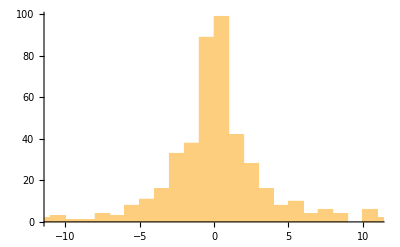
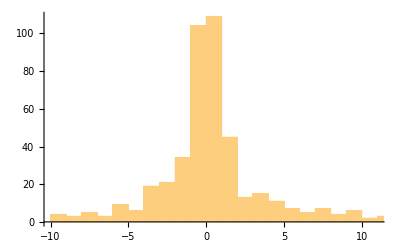
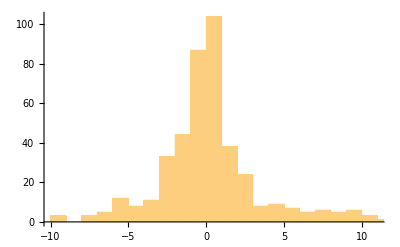
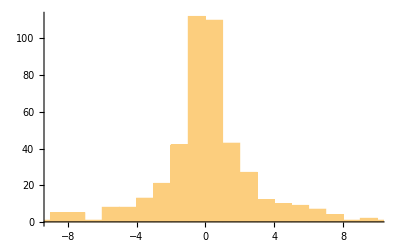
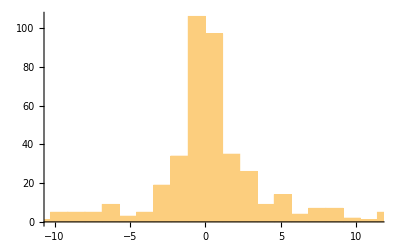
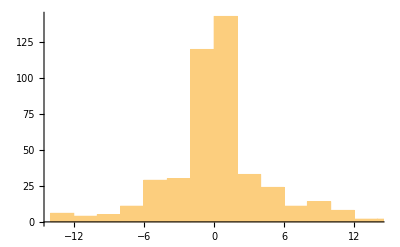
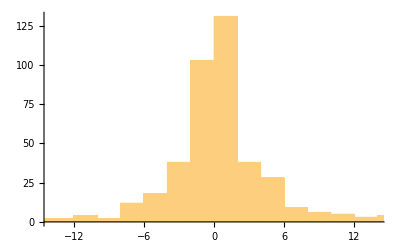
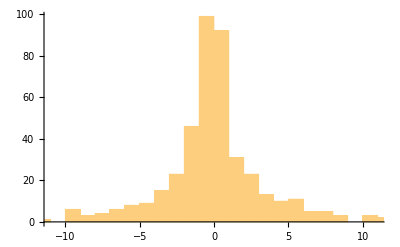

```mathematica
Map[Histogram,Out@27]
```

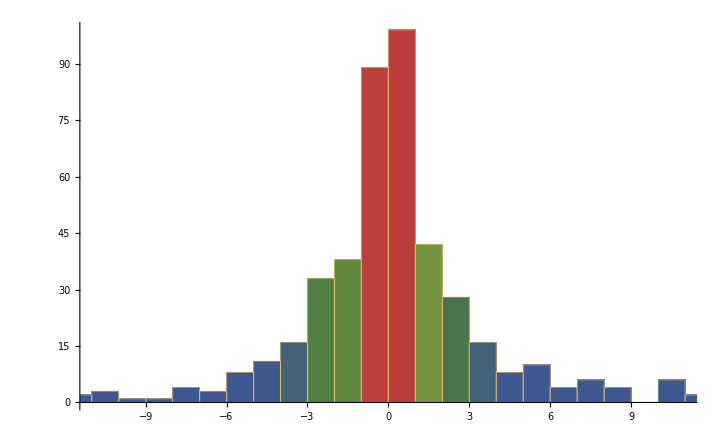
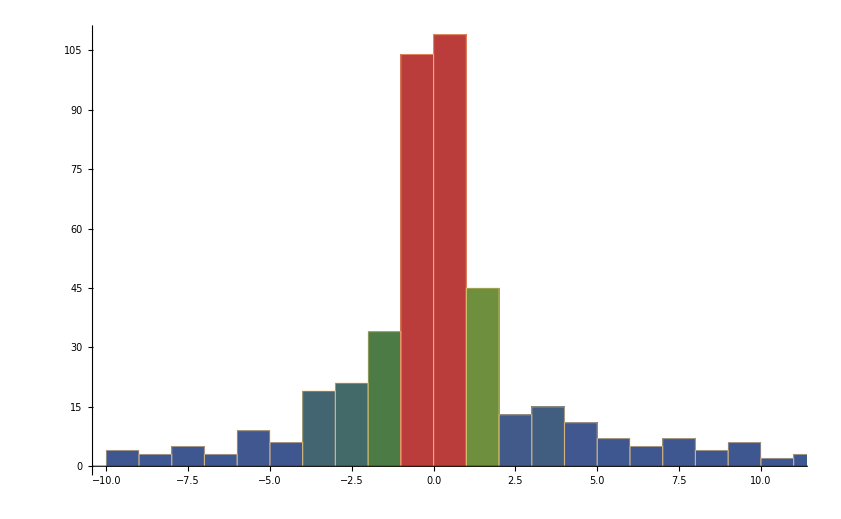
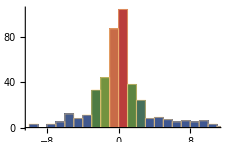
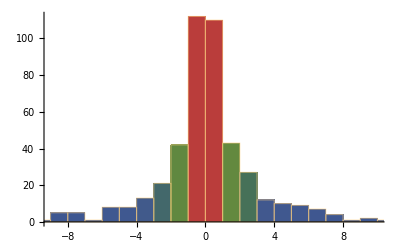
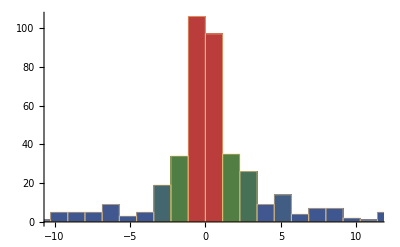
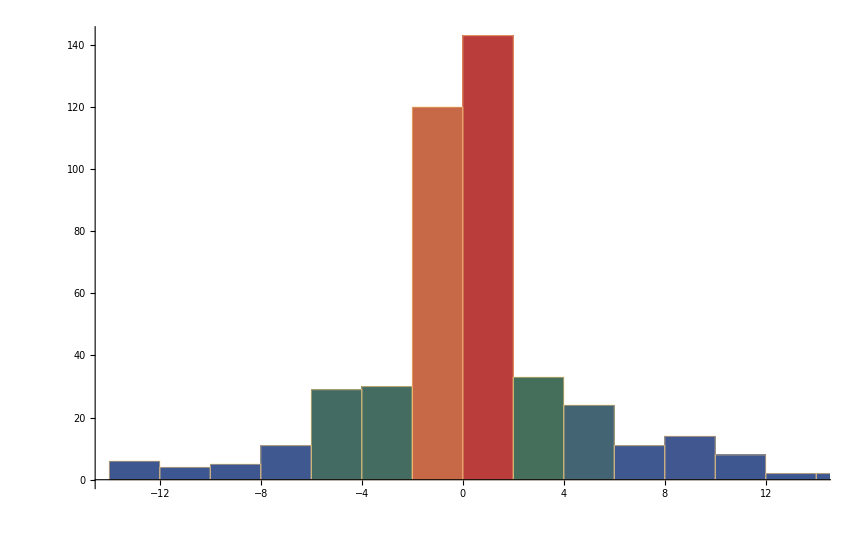
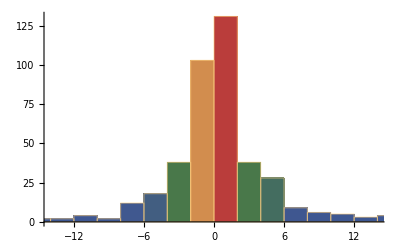
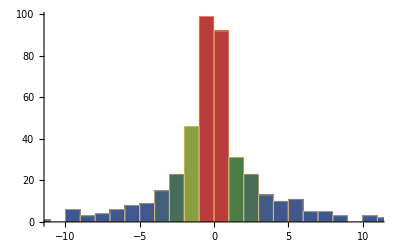

```mathematica
Map[Histogram[#, ColorFunction->"DarkRainbow"]&,Out@27]
```

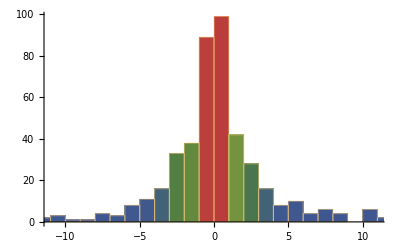
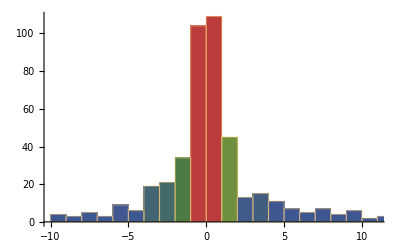
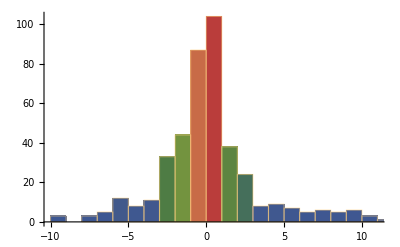
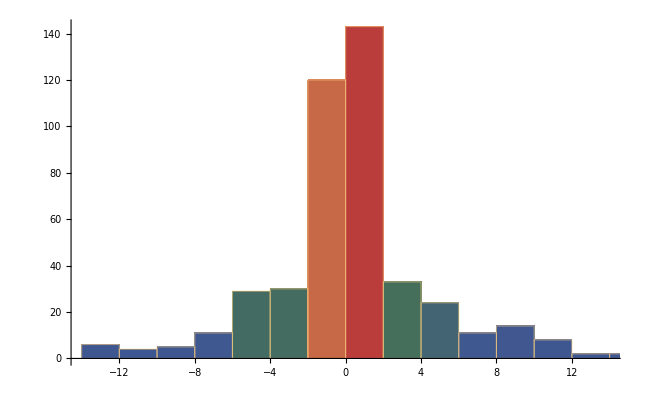
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
Map[Histogram[#, ColorFunction->"DarkRainbow"]&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]
]
```

```mathematica
Entropy@Out@27
```

Log[12]

```mathematica
N[Log[12]]
```

2.48491

```mathematica
Table[Entropy@Range@i, {i, 1, 10}]
```

{0,Log[2],Log[3],Log[4],Log[5],Log[6],Log[7],Log[8],Log[9],Log[10]}

```mathematica
Entropy@{a}
```

0

```mathematica
Entropy@{b}
```

0

```mathematica
Entropy@{a,b}
```

Log[2]

```mathematica
Entropy@{a,b,c}
```

Log[3]

```mathematica
TakeLargestBy[
Table[i->Entropy@Range@i, {i, 1, 100}], Last, 30]
```

{100→Log[100],99→Log[99],98→Log[98],97→Log[97],96→Log[96],95→Log[95],94→Log[94],93→Log[93],92→Log[92],91→Log[91],90→Log[90],89→Log[89],88→Log[88],87→Log[87],86→Log[86],85→Log[85],84→Log[84],83→Log[83],82→Log[82],81→Log[81],80→Log[80],79→Log[79],78→Log[78],77→Log[77],76→Log[76],75→Log[75],74→Log[74],73→Log[73],72→Log[72],71→Log[71]}

```mathematica
Grid@
TakeLargestBy[
Table[{i,Entropy@Range@i}, {i, 1, 100}], Last, 30]
```

100 | Log[100]
99 | Log[99]
98 | Log[98]
97 | Log[97]
96 | Log[96]
95 | Log[95]
94 | Log[94]
93 | Log[93]
92 | Log[92]
91 | Log[91]
90 | Log[90]
89 | Log[89]
88 | Log[88]
87 | Log[87]
86 | Log[86]
85 | Log[85]
84 | Log[84]
83 | Log[83]
82 | Log[82]
81 | Log[81]
80 | Log[80]
79 | Log[79]
78 | Log[78]
77 | Log[77]
76 | Log[76]
75 | Log[75]
74 | Log[74]
73 | Log[73]
72 | Log[72]
71 | Log[71]

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
Map[Histogram[#, ColorFunction->"DarkRainbow"]&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]
```

```mathematica
Map[Entropy,Out@27]
```

{1/476 (-54 Log[2]-6 Log[3])+Log[476],1/473 (-48 Log[2]-18 Log[3]-4 Log[4])+Log[473],1/464 (-42 Log[2]-3 Log[3]-8 Log[8])+Log[464],1/486 (-56 Log[2]-9 Log[3]-4 Log[4])+Log[486],1/444 (-36 Log[2]-6 Log[3])+Log[444],1/487 (-38 Log[2]-3 Log[3]-5 Log[5])+Log[487],1/448 (-40 Log[2]-6 Log[3])+Log[448],1/463 (-42 Log[2]-12 Log[3]-4 Log[4])+Log[463],1/444 (-36 Log[2]-3 Log[3])+Log[444],1/421 (-34 Log[2]-5 Log[5])+Log[421],1/479 (-68 Log[2]-15 Log[3])+Log[479],1/454 (-34 Log[2]-12 Log[3])+Log[454]}

```mathematica
Map[Composition[N,Entropy],Out@27]
```

{6.07294,6.03522,6.03419,6.07459,6.02478,6.11089,6.02819,6.0344,6.0322,5.96754,6.0389,6.03715}

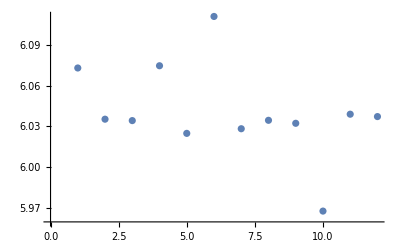

```mathematica
ListPlot[{6.072935456159476,6.035223795875901,6.034187244504357,6.07458531082673,6.024777327675093,6.110887081420469,6.028191533856042,6.034399394276267,6.032200383679607,5.967539737004926,6.038896437477517,6.0371492870214025}]
```

```mathematica
TracePrint[(2+3)^2]
```

(2+3)^2

Power

2+3

Plus

2

3

5

2

5^2

25

25

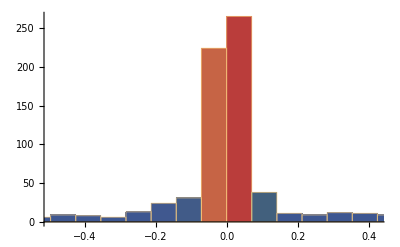
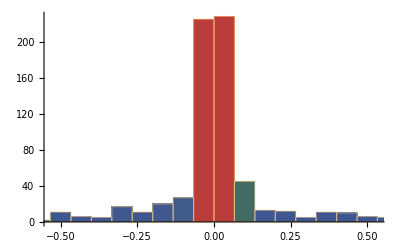
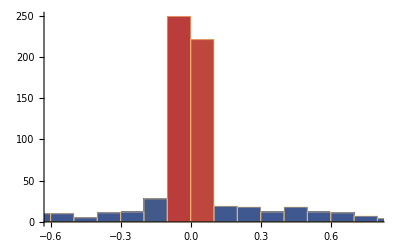
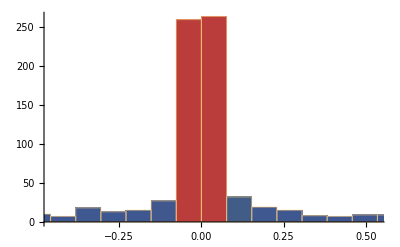
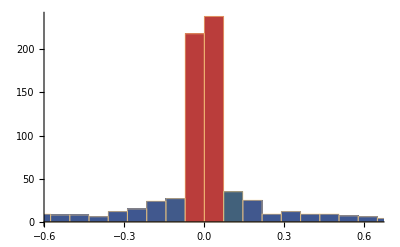
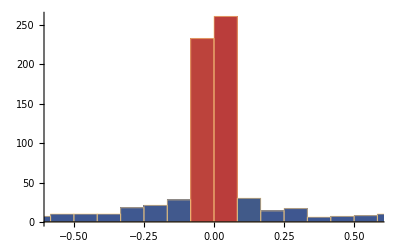
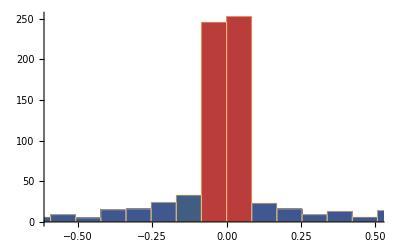
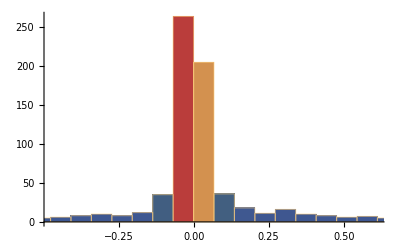

```mathematica
With[{list=FinancialData["NASDAQ:AAPL", "Price", All]},
Map[Histogram[#, ColorFunction->"DarkRainbow"]&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]
]
```

```mathematica
With[{list=FinancialData["NASDAQ:AAPL", "Price", All]},
Map[Entropy,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

{1/814 (-124 Log[2]-48 Log[3]-20 Log[4]-30 Log[5]-18 Log[9]-27 Log[27])+Log[814],1/805 (-82 Log[2]-51 Log[3]-16 Log[4]-15 Log[5]-6 Log[6]-9 Log[9]-25 Log[25])+Log[805],1/747 (-76 Log[2]-45 Log[3]-40 Log[4]-15 Log[5]-28 Log[28])+Log[747],1/851 (-104 Log[2]-36 Log[3]-28 Log[4]-20 Log[5]-12 Log[6]-9 Log[9]-10 Log[10]-31 Log[31])+Log[851],1/810 (-86 Log[2]-36 Log[3]-40 Log[4]-15 Log[5]-12 Log[6]-7 Log[7]-8 Log[8]-31 Log[31])+Log[810],1/824 (-100 Log[2]-57 Log[3]-24 Log[4]-10 Log[5]-12 Log[6]-14 Log[7]-26 Log[26])+Log[824],1/816 (-112 Log[2]-48 Log[3]-24 Log[4]-15 Log[5]-12 Log[6]-9 Log[9]-25 Log[25])+Log[816],1/802 (-108 Log[2]-45 Log[3]-32 Log[4]-10 Log[5]-12 Log[6]-32 Log[32])+Log[802],1/841 (-108 Log[2]-57 Log[3]-32 Log[4]-15 Log[5]-12 Log[6]-7 Log[7]-31 Log[31])+Log[841],1/771 (-108 Log[2]-45 Log[3]-20 Log[4]-35 Log[5]-18 Log[6]-7 Log[7]-29 Log[29])+Log[771],1/840 (-96 Log[2]-57 Log[3]-20 Log[4]-25 Log[5]-6 Log[6]-9 Log[9]-39 Log[39])+Log[840],1/776 (-78 Log[2]-57 Log[3]-28 Log[4]-15 Log[5]-12 Log[6]-7 Log[7]-24 Log[24])+Log[776]}

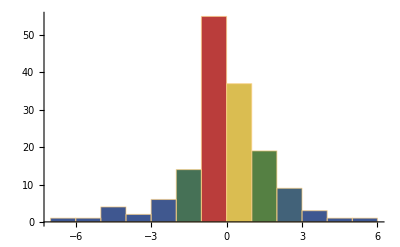
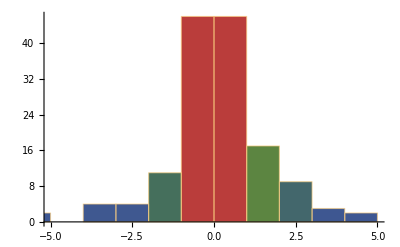
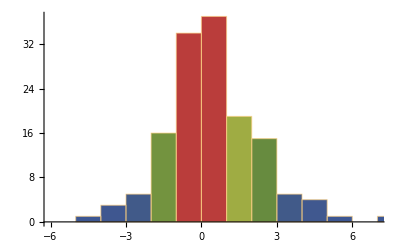
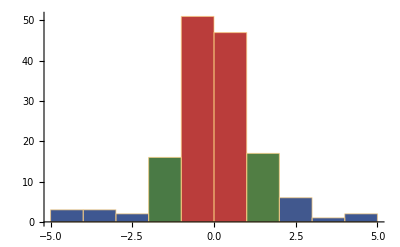
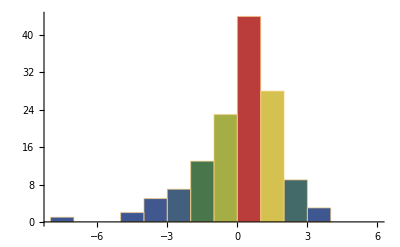
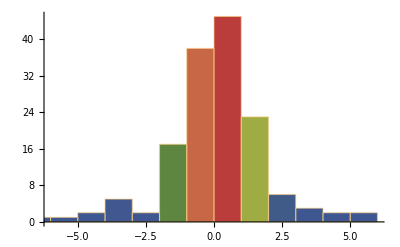
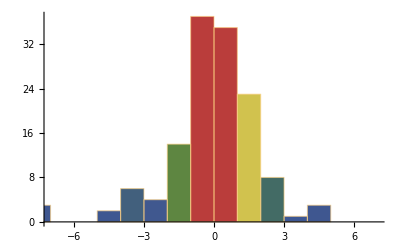
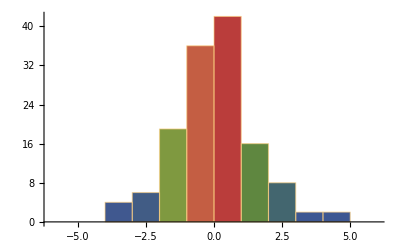

```mathematica
With[{list=FinancialData["NASDAQ:FB", "Price", All]},
Map[Histogram[#, ColorFunction->"DarkRainbow"]&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

```mathematica
With[{list=FinancialData["NASDAQ:FB", "Price", All]},
Map[Entropy,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

{1/158 (-20 Log[2]-3 Log[3]-4 Log[4])+Log[158],-(16 Log[2])/151+Log[151],-(4 Log[2])/147+Log[147],-Log[2]/11+Log[154],-Log[2]/70+Log[140],-(18 Log[2])/155+Log[155],-(5 Log[2])/71+Log[142],1/144 (-8 Log[2]-6 Log[3])+Log[144],-(4 Log[2])/47+Log[141],-(2 Log[2])/33+Log[132],-(4 Log[2])/37+Log[148],-(6 Log[2])/143+Log[143]}

```mathematica
With[{list=FinancialData["NASDAQ:FB", "Price", All]},
Map[Composition[N,Entropy],
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

{4.9189,4.94383,4.97157,4.97394,4.93174,4.96293,4.90701,4.88553,4.88977,4.84079,4.92228,4.93376}

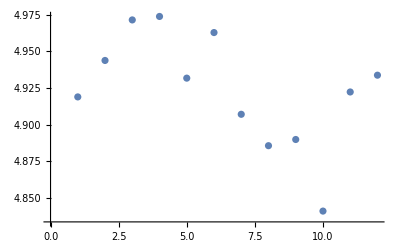

```mathematica
ListPlot[{4.918899096813784,4.943833777947646,4.971571439008398,4.973939222362725,4.931740320029876,4.962930605628414,4.907013875871687,4.885529610850388,4.8897686409688115,4.840793002552434,4.92227744343331,4.933761531774874}]
```

```mathematica
With[{list=FinancialData["NASDAQ:MFSF", "Price", All]},
Map[Histogram[#, ColorFunction->"DarkRainbow"]&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[Dates],$Failed[Values]} cannot be transposed.

GatherBy::list: List expected at position 1 in GatherBy[Transpose[{$Failed[Dates],$Failed[Values]}],DateValue[First[#1],MonthName]&].

Table::iterb: Iterator {i,GatherBy[Transpose[{$Failed[Dates],$Failed[Values]}],DateValue[First[#1],MonthName]&]} does not have appropriate bounds.

Table::nliter: Non-list iterator (Histogram[#1,ColorFunction→DarkRainbow]&)[{i,GatherBy[Transpose[{$Failed[Dates],$Failed[Values]}],DateValue[First[#1],MonthName]&]}] at position 2 does not evaluate to a real numeric value.

Table[(Histogram[#1,ColorFunction→DarkRainbow]&)[Differences[Last/@i]],(Histogram[#1,ColorFunction→DarkRainbow]&)[{i,GatherBy[Transpose[{$Failed[Dates],$Failed[Values]}],DateValue[First[#1],MonthName]&]}]]

```mathematica
With[{list=FinancialData["NASDAQ:FB", "Price", All]},
Map[Histogram[#, ColorFunction->"DarkRainbow"]&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

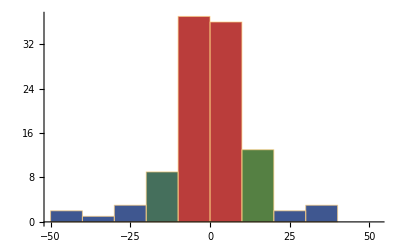
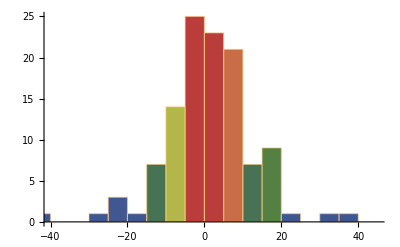
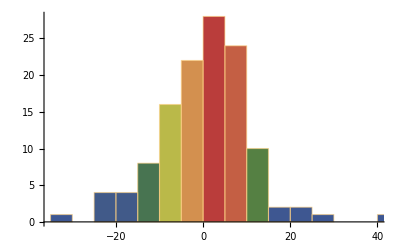
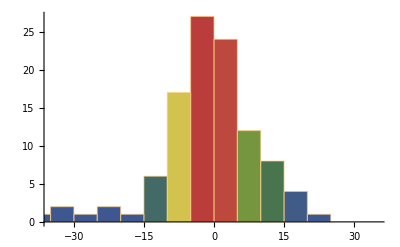
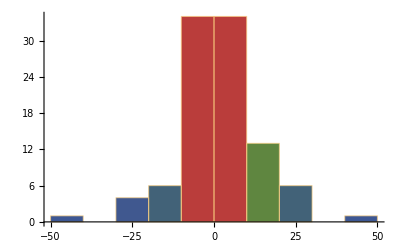
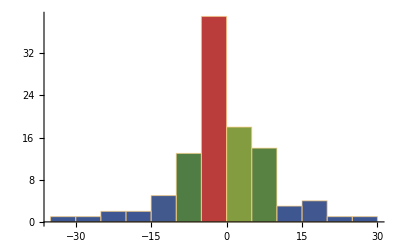
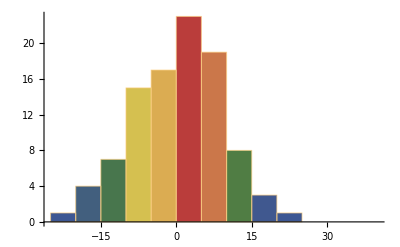
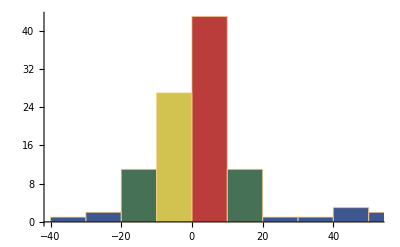

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Map[Histogram[#, ColorFunction->"DarkRainbow"]&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Map[{Entropy@#,Histogram[#, ColorFunction->"DarkRainbow"]}&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

{{-Log[2]/55+Log[110],-Graphics-},{Log[121],-Graphics-},{Log[127],-Graphics-},{Log[110],-Graphics-},{Log[103],-Graphics-},{-(6 Log[2])/109+Log[109],-Graphics-},{Log[101],-Graphics-},{Log[108],-Graphics-},{Log[101],-Graphics-},{Log[102],-Graphics-},{Log[99],-Graphics-},{Log[94],-Graphics-}}

```mathematica
Grid@
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Map[{Histogram[#, ColorFunction->"DarkRainbow"],N@Entropy@#,Mean@#, Variance@#, Kurtosis@#, Skewness@#}&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```

-Graphics- | 4.68788 | 5.60 $ | 1114.6 $^2 | 29.6531 | 4.65014
-Graphics- | 4.79579 | 5.15 $ | 1087.94 $^2 | 23.6558 | 3.76824
-Graphics- | 4.84419 | 4.52 $ | 651.941 $^2 | 30.7118 | 4.78782
-Graphics- | 4.70048 | 4.45 $ | 1663.19 $^2 | 30.5687 | 4.99968
-Graphics- | 4.63473 | 6.18 $ | 798.557 $^2 | 25.6883 | 4.14454
-Graphics- | 4.65319 | 6.00 $ | 1297.4 $^2 | 37.8606 | 5.56293
-Graphics- | 4.61512 | 6.12 $ | 1118.31 $^2 | 32.4373 | 5.2714
-Graphics- | 4.68213 | 4.72 $ | 862.188 $^2 | 21.7003 | 3.51197
-Graphics- | 4.61512 | 5.35 $ | 1196.48 $^2 | 40.1048 | 5.6642
-Graphics- | 4.62497 | 4.93 $ | 1290.08 $^2 | 35.6275 | 5.41433
-Graphics- | 4.59512 | 5.99 $ | 1495.75 $^2 | 30.9704 | 4.27897
-Graphics- | 4.54329 | 6.31 $ | 1979.02 $^2 | 40.1605 | 5.55753

```mathematica
Grid[
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Map[{Histogram[#, ColorFunction->"DarkRainbow"],N@Entropy@#,Mean@#, Variance@#, Kurtosis@#, Skewness@#}&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]],
Frame->All]
```

-Graphics- | 4.68788 | 5.60 $ | 1114.6 $^2 | 29.6531 | 4.65014
-Graphics- | 4.79579 | 5.15 $ | 1087.94 $^2 | 23.6558 | 3.76824
-Graphics- | 4.84419 | 4.52 $ | 651.941 $^2 | 30.7118 | 4.78782
-Graphics- | 4.70048 | 4.45 $ | 1663.19 $^2 | 30.5687 | 4.99968
-Graphics- | 4.63473 | 6.18 $ | 798.557 $^2 | 25.6883 | 4.14454
-Graphics- | 4.65319 | 6.00 $ | 1297.4 $^2 | 37.8606 | 5.56293
-Graphics- | 4.61512 | 6.12 $ | 1118.31 $^2 | 32.4373 | 5.2714
-Graphics- | 4.68213 | 4.72 $ | 862.188 $^2 | 21.7003 | 3.51197
-Graphics- | 4.61512 | 5.35 $ | 1196.48 $^2 | 40.1048 | 5.6642
-Graphics- | 4.62497 | 4.93 $ | 1290.08 $^2 | 35.6275 | 5.41433
-Graphics- | 4.59512 | 5.99 $ | 1495.75 $^2 | 30.9704 | 4.27897
-Graphics- | 4.54329 | 6.31 $ | 1979.02 $^2 | 40.1605 | 5.55753

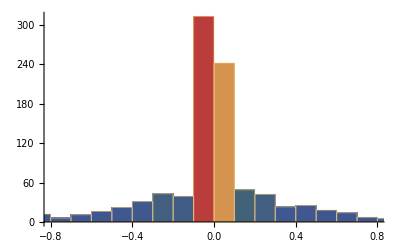
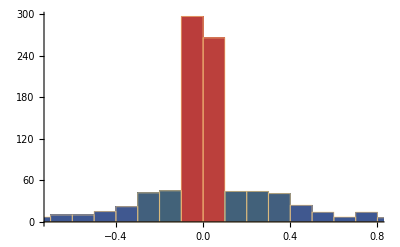
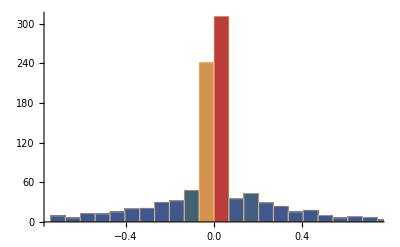
-Graphics- | 6.18858 | 0.05 $ | 3.91558 $^2 | 260.644 | 0.150566
-Graphics- | 6.217 | 0.05 $ | 3.59076 $^2 | 254.135 | -1.15464
-Graphics- | 6.19626 | 0.05 $ | 3.81607 $^2 | 285.614 | -7.93732
-Graphics- | 6.24196 | 0.05 $ | 3.45207 $^2 | 191.85 | 9.66353
-Graphics- | 6.33271 | 0.04 $ | 1.81688 $^2 | 150.661 | -4.73689
-Graphics- | 6.14457 | 0.05 $ | 1.69934 $^2 | 64.3103 | -0.0794188
-Graphics- | 6.12737 | 0.05 $ | 1.66152 $^2 | 83.708 | 2.96618
-Graphics- | 6.19073 | 0.05 $ | 2.09452 $^2 | 84.6281 | -0.928198
-Graphics- | 6.09369 | 0.06 $ | 2.37647 $^2 | 88.0345 | 2.62864
-Graphics- | 6.25157 | 0.05 $ | 3.40588 $^2 | 219.713 | -3.73886
-Graphics- | 6.20841 | 0.05 $ | 3.90631 $^2 | 237.356 | -1.22471
-Graphics- | 6.12355 | 0.04 $ | 3.68175 $^2 | 213.829 | 3.6932

```mathematica
Grid@
With[{list=FinancialData["NASDAQ:INTC", "Price", All]},
Map[{Histogram[#, ColorFunction->"DarkRainbow"],N@Entropy@#,Mean@#, Variance@#, Kurtosis@#, Skewness@#}&,
Table[
Differences@
Map[Last,i],
{i, GatherBy[
Transpose[{list["Dates"],list["Values"]}],
DateValue[First@#, "MonthName"]&]}]]]
```